```mathematica
Clear["`*"];
```

```mathematica
csv=Import["/home/bczhc/t/aom-av1-crf-test/csv.csv"][[2;;]];
```

```mathematica
sources=DeleteDuplicates[#[[1]]&/@csv]
```

{animation1.mkv,animation2.mkv,animation3.mkv,camera.mkv,game.mkv,screenrecord.mkv}

```mathematica
data=Module[{selectF,source},
source=#1;
selectF[x_]:=x[[1]]==source;
Select[csv,selectF]
]&/@sources;
```

```mathematica
crfVmafData=(#[[2;;3]]&/@#)&/@data;
```

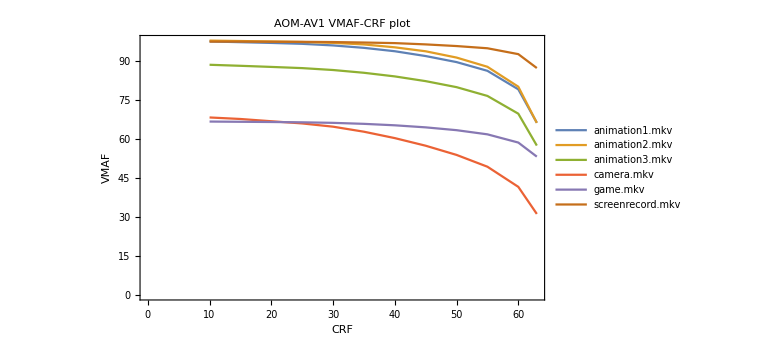

```mathematica
ListLinePlot[crfVmafData,PlotLegends->sources,ImageSize->Large,PlotLabel->"AOM-AV1 VMAF-CRF plot",FrameLabel->{"CRF","VMAF"},Frame->True]
```

```mathematica
Manipulate[ListLinePlot[({#[[2]],#[[6]]/1048576}&/@#)&/@data,ImageSize->Large,FrameLabel->{"CRF","Bitrate (MiB)"},Frame->True,PlotLabel->"Bitrate-CRF plot", PlotLegends->sources,ScalingFunctions->scaling],{scaling,{"Linear","Log"}},SaveDefinitions->True]
```